## Lesson

Frame an expression in different styles:

```mathematica
Framed[2^100,Background->LightYellow,FrameStyle->LightGray]
```

1267650600228229401496703205376

Label an expression:

```mathematica
Labeled[Style[2^100,Background->Yellow],Style["a big number",Italic,Orange]]
```

1267650600228229401496703205376a big number

Add tooltip to expression:

```mathematica
Tooltip["Potato","A very good food."]
```

Potato

Add callouts to expressions:

```mathematica
ListPlot[Table[Callout[Prime[n],Prime[n]],{n,15}]]
```

-Graphics-

Add legends to expressions:

```mathematica
PieChart[{Legended[1,"one"],Legended[2,"two"],Legended[3,Pink],Legended[4,Yellow],2,2}]
```

-Graphics-

Create row (also equivalent: column, grid):

```mathematica
Row[{Yellow,Pink,Cyan}]
```

RGBColor[1, 1, 0]RGBColor[1, 0.5, 0.5]RGBColor[0, 1, 1]

Create create grid graphic (also equivalent: row, column):

```mathematica
GraphicsGrid[Table[PieChart[RandomReal[10,5]],3,6],Frame->All]
```

-Graphics-

## Questions

Q1. Make a list of numbers up to 100, with even numbers on yellow and odd numbers on light gray.

```mathematica
Style[#,Background->If[EvenQ[#],Yellow,LightGray]]&/@Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

Q2. Make a list of numbers up to 100, with primes framed.

```mathematica
If[PrimeQ[#],Framed[#],#]&/@Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

Q3. Make a list of numbers up to 100, with primes framed and labeled in light gray with their values modulo 4.

```mathematica
If[PrimeQ[#],Labeled[Framed[#],Style[Mod[#,4],LightGray]],#]&/@Range[100]
```

{1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100}

Q4. Create a 3×6 GraphicsGrid of randomly colored disks.

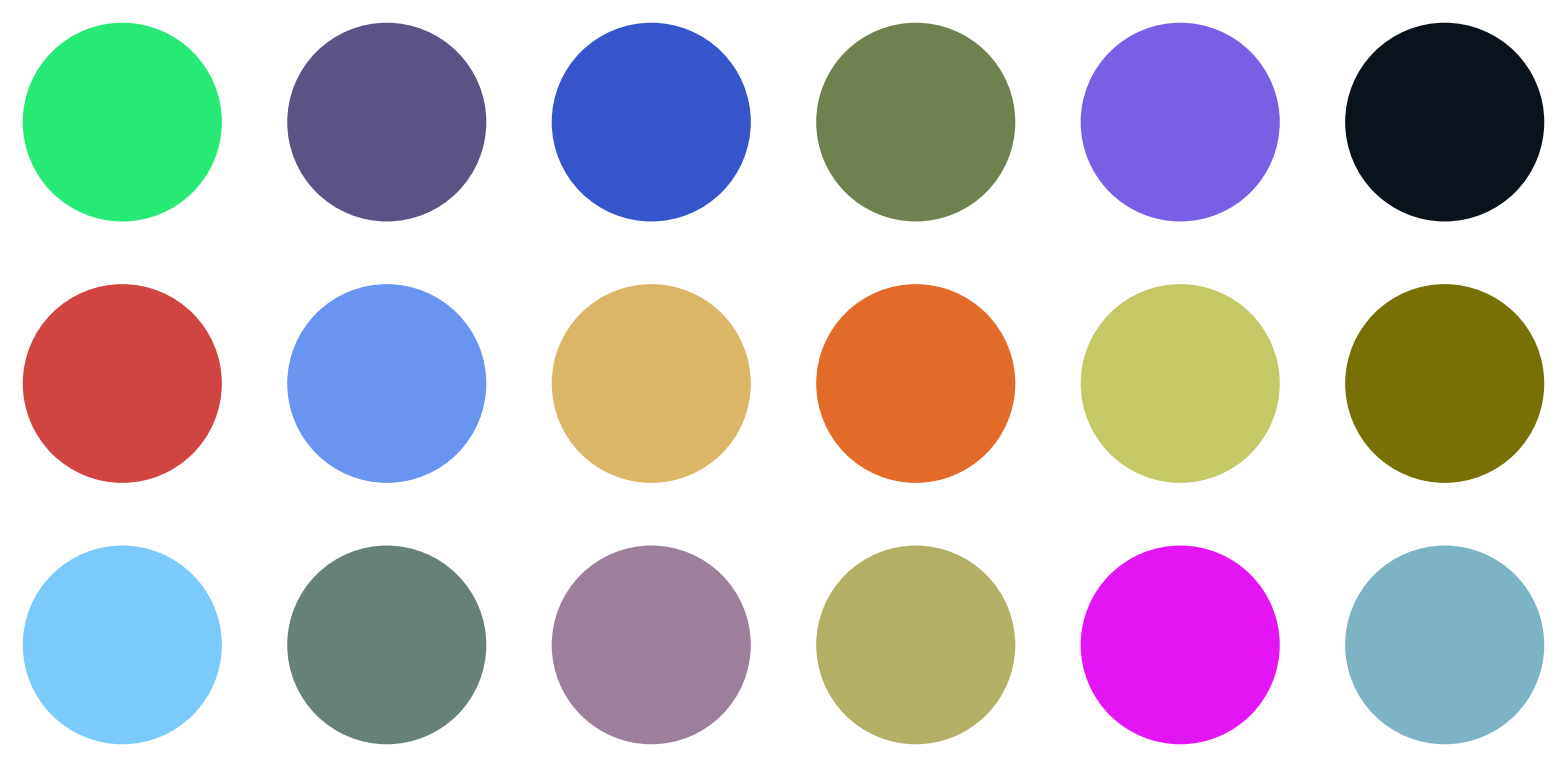

```mathematica
GraphicsGrid[Table[Graphics[Style[Disk[],RandomColor[]]],3,6]]
```

Q5. Make a pie chart of the GDPs of the countries in the G5, labeling each wedge.

```mathematica
PieChart[#["GDP"]->CommonName[#]&/@EntityList[EntityClass["Country","GroupOf5"]]]
```

-Graphics-

Q6. Make a pie chart of the populations of the countries in the G5, giving a legend for each wedge.

```mathematica
PieChart[Legended[#["Population"]->CommonName[#],CommonName[#]]&/@EntityList[EntityClass["Country","GroupOf5"]]]
```

-Graphics-

Q7. Make a 5×5 GraphicsGrid of pie charts that give the relative frequencies of digits in 2^n with n starting at 1.

```mathematica
GraphicsGrid[Partition[PieChart[IntegerDigits[2^#]]&/@Range[25],5]]
```

-Graphics-

Q8. Make a graphics row of word clouds for Wikipedia articles on the G5 countries.

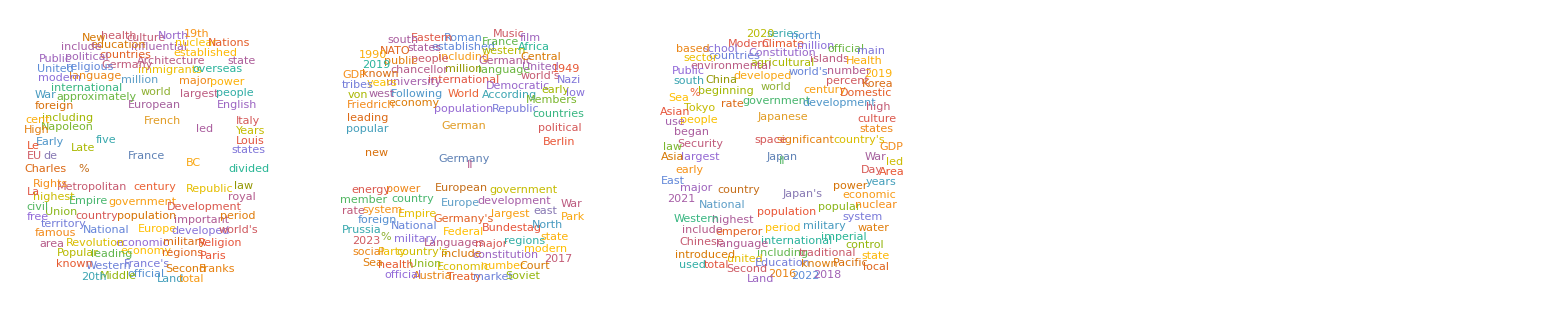

```mathematica
GraphicsRow[WordCloud[WikipediaData[CommonName[#]]]&/@EntityList[EntityClass["Country","GroupOf5"]]]
```